## Generator of Legendre-Chebyshev quadrature

```mathematica
$NumberMarks=False;
```

```mathematica
symboliclegendre[n_,x_]:=Solve[LegendreP[n,x]==0,Reals]
legendreprime[n_,a_]:=D[LegendreP[n,x],x]/.x->a
weights[n_,x_]:=π/((1-x^2) legendreprime[n,x]^2) (* sum of weights over all ordinates = 4π *)
```

### Generate quadrature file

```mathematica
SetDirectory["~/."];

(*how many terms should be generated*)
Nmax=30;

(*what numerical precision is desired?*)
precision=16;

(*generate Subscript[S, 2],Subscript[S, 4],...,Subscript[S, Nmax]*)
str=OpenWrite["lgvalues.txt"];
Write[str,"abcissae"];
Do[Write[str];Write[str,n];Write[str];
(* write sorted roots of n-th order Legendre polynomial *)
nlist=symboliclegendre[n,x];
xnlist=x/.nlist;
μ=Sort[xnlist,#1>#2&];
Do[Write[str,N[Part[μ,i],precision]],{i,Length[μ]}];,{n,2,Nmax,2}];
Write[str,"weights"];
Do[Write[str];Write[str,n];Write[str];
(* write weights corresponding to sorted roots of n-th order Legendre polynomial *)
slist:=symboliclegendre[n,x];
xslist=x/.slist;
μ=Sort[xslist,#1>#2&];
Do[Write[str,N[weights[n,Part[μ,i]],precision]],{i,Length[μ]}];,{n,2,Nmax,2}];
Close[str];

ResetDirectory[];
```

### Testing

```mathematica
Nmax = 8;(* SN order *)
```

```mathematica
M=Nmax(Nmax+2)/8 (* number of directions in principal octant *)
```

10

```mathematica
n=Nmax/2 (* number of levels in principal octant *)
```

4

```mathematica
Sum[i,{i,1,n}]
```

10

```mathematica
measS=4π;(* sum of weights over all directions *)
```

```mathematica
xlist=x/.symboliclegendre[Nmax,x];
```

```mathematica
μ=Sort[xlist,#1>#2&];
```

```mathematica
μ//N
```

{0.96029,0.796666,0.525532,0.183435,-0.183435,-0.525532,-0.796666,-0.96029}

```mathematica
w=With[{n=Length[μ]},Table[weights[n,μ⟦i⟧],{i,1,n}]//N]
```

{0.159009,0.349315,0.492769,0.569702,0.569702,0.492769,0.349315,0.159009}

```mathematica
ω=Table[(2l-2i+1)/(2l)π/2,{l,1,n},{i,1,l}];
```

```mathematica
pw=Table[w⟦l⟧/l,{l,1,n}];(* point weights: uniform distribution of w between l points in level l *)
```

```mathematica
pw
```

{0.159009,0.174658,0.164256,0.142426}

```mathematica
1/measS 4Total[Flatten@Table[w[[l]],{l,1,Nmax}]]
```

1.

```mathematica
1/measS 8 Sum[l pw[[l]],{l,1,n}]
```

1.

```mathematica
1/measS 8Table[Sum[pw⟦l⟧μ⟦l⟧^o,{l,1,n},{j,1,l}],{o,2,Nmax,2}]
```

{0.333333,0.2,0.142857,0.111111}

```mathematica
1/measS 4Table[Sum[w⟦l⟧μ⟦l⟧^o,{l,1,Nmax}],{o,1,Nmax,2}]
```

{2.65046×10^-17,0.,-8.83487×10^-18,4.41744×10^-18}

```mathematica
ξ=Map[Cos[#]&,ω,{2}];
η=Map[Sin[#]&,ω,{2}];
```

```mathematica
Length[ξ]
```

4

```mathematica
z={};
```

```mathematica
Do[z=Join[z,{{√(1-μ⟦l⟧^2)ξ⟦l,i⟧,√(1-μ⟦l⟧^2)η⟦l,i⟧,μ⟦l⟧}}],{l,1,n},{i,1,l}]
```

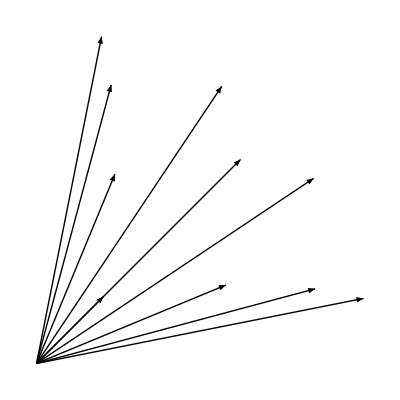

```mathematica
Graphics[Arrow[{{0,0},#}]&/@z[[All,1;;2]]]
```

```mathematica
ListPointPlot3D[z,PlotRange->{{0,1},{0,1},{0,1}},AspectRatio->Automatic,BoxRatios->Automatic,AxesLabel->{"x","y","z"},PlotStyle->PointSize[0.02]]
```

-Graphics3D-

### Reflections

```mathematica
normals={{0,-1,0},{1,0,0},{0,0,1}};
```

```mathematica
Reflected[Ω_,n_]:=Ω-2n(Ω.n);
```

```mathematica
zr1x=Map[Reflected[#,normals⟦1⟧]&,N[z]];
zr1y=Map[Reflected[#,normals⟦2⟧]&,N[z]];
zr1z=Map[Reflected[#,normals⟦3⟧]&,N[z]];
```

```mathematica
ListPointPlot3D[{z⟦All,All⟧,zr1z⟦All,All⟧},PlotRange->{{-1,1},{-1,1},{-1,1}},AspectRatio->Automatic,BoxRatios->Automatic,AxesLabel->{"x","y","z"},PlotStyle->PointSize[0.02]]
```

-Graphics3D-

```mathematica
ListPointPlot3D[{z⟦1;;2,All⟧,zr1x⟦1;;2,All⟧},PlotRange->{{-1,1},{-1,1},{0,1}},AspectRatio->Automatic,BoxRatios->Automatic,AxesLabel->{"x","y","z"},PlotStyle->PointSize[0.02]]
```

-Graphics3D-

```mathematica
ListPointPlot3D[{z,zr1x,zr1y},PlotRange->{{-1,1},{-1,1},{0,1}},AspectRatio->Automatic,BoxRatios->Automatic,AxesLabel->{"x","y","z"},PlotStyle->PointSize[0.02]]
```

-Graphics3D-

```mathematica
zr2x=Map[Reflected[#,normals⟦1⟧]&,N[zr1x]];
zr2y=Map[Reflected[#,normals⟦2⟧]&,N[zr1x]];
zr2z=Map[Reflected[#,normals⟦3⟧]&,N[zr1x]];
```

```mathematica
ListPointPlot3D[{zr1x⟦All,All⟧,zr2x⟦All,All⟧},PlotRange->{{-1,1},{-1,1},{0,1}},AspectRatio->Automatic,BoxRatios->Automatic,AxesLabel->{"x","y","z"},PlotStyle->PointSize[0.02]]
```

-Graphics3D-

```mathematica
ListPointPlot3D[{zr1x⟦All,All⟧,zr2y⟦All,All⟧},PlotRange->{{-1,1},{-1,1},{0,1}},AspectRatio->Automatic,BoxRatios->Automatic,AxesLabel->{"x","y","z"},PlotStyle->PointSize[0.02]]
```

-Graphics3D-

```mathematica
ListPointPlot3D[{zr1x,zr2z},PlotRange->{{-1,1},{-1,1},{-1,1}},AspectRatio->Automatic,BoxRatios->Automatic,AxesLabel->{"x","y","z"},PlotStyle->PointSize[0.02]]
```

-Graphics3D-

```mathematica
Q1[Ω_]:={Ω⟦1⟧,Ω⟦2⟧,Ω⟦3⟧};
Q2[Ω_]:={-Ω⟦1⟧,Ω⟦2⟧,Ω⟦3⟧};
Q3[Ω_]:={-Ω⟦1⟧,-Ω⟦2⟧,Ω⟦3⟧};
Q4[Ω_]:={Ω⟦1⟧,-Ω⟦2⟧,Ω⟦3⟧};
Q12[Ω_]:={Ω⟦1⟧,Ω⟦2⟧,-Ω⟦3⟧};
Q22[Ω_]:={-Ω⟦1⟧,Ω⟦2⟧,-Ω⟦3⟧};
Q32[Ω_]:={-Ω⟦1⟧,-Ω⟦2⟧,-Ω⟦3⟧};
Q42[Ω_]:={Ω⟦1⟧,-Ω⟦2⟧,-Ω⟦3⟧};
```

```mathematica
zr1y-Map[Q2[#]&,N[z]]
```

{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}

```mathematica
zr1x-Map[Q4[#]&,N[z]]
```

{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}

```mathematica
zr2z-Map[Q42[#]&,N[z]]
```

{{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.},{0.,0.,0.}}

```mathematica
Graphics3D[{
{Thickness[0.005],Line[z,VertexColors->ColorData["TemperatureMap"]/@Rescale@Range@Length@z]},
{Thickness[0.005],Line[zr2,VertexColors->ColorData["Rainbow"]/@Rescale@Range@Length@z]},
{Thickness[0.005],Line[Map[Q3[#]&,N[z]],VertexColors->ColorData["FruitPunchColors"]/@Rescale@Range@Length@z]},
{Thickness[0.005],Line[zr1,VertexColors->ColorData["GreenPinkTones"]/@Rescale@Range@Length@z]}},Axes->True,AxesLabel->{"x","y","z"}]
```

-Graphics3D-

```mathematica
Grid[{N@z,zr1,zr2},Frame->All]
```

{0.359475,0.359475,0.861136} | {0.359888,0.868846,0.339981} | {0.868846,0.359888,0.339981}
{0.359475,-0.359475,0.861136} | {0.359888,-0.868846,0.339981} | {0.868846,-0.359888,0.339981}
{-0.359475,0.359475,0.861136} | {-0.359888,0.868846,0.339981} | {-0.868846,0.359888,0.339981}